```mathematica
(*Quit[]*)
```

```mathematica
SetDirectory["/Users/oliveratkinson/Dropbox/cascade_interference/model"]
```

/Users/oliveratkinson/Dropbox/cascade_interference/model

```mathematica
(*HXSWG cross sections*)
hxswg1=Import["hxswg_14.dat"];
hxswg14={};
Do[hxswg14=Append[hxswg14,{hxswg1[[i,1]],hxswg1[[i,2]]*1000}],{i,1,Length[hxswg1]}]
```

```mathematica
crosssec=Interpolation[hxswg14]
```

InterpolatingFunction[…]

```mathematica
(*Importing the branching ratios from hdecay, interpolating to generate smooth functions*)
widths=Import["brs_hdecay.dat"];
width={};
wwbr={};
zzbr={};
ttbr={};
Do[
If[widths[[i,1]]>90,width=Append[width,{widths[[i,1]],widths[[i,5]]}];
wwbr=Append[wwbr,{widths[[i,1]],widths[[i,3]]}];
zzbr=Append[zzbr,{widths[[i,1]],widths[[i,4]]}]];
ttbr=Append[ttbr,{widths[[i,1]],widths[[i,2]]}],{i,1,Length[widths]}]
```

```mathematica
wwBRs=Interpolation[wwbr];
zzBRs=Interpolation[zzbr];
ttBRs=Interpolation[ttbr];
hwidth=Interpolation[width];
```

```mathematica
wwBRs=Interpolation[wwbr]
zzBRs=Interpolation[zzbr]
ttBRs=Interpolation[ttbr]
hwidth=Interpolation[width]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

InterpolatingFunction[…]

«1 more identical outputs»

```mathematica
(*Checking*)
hwidth[125]
```

0.00407119

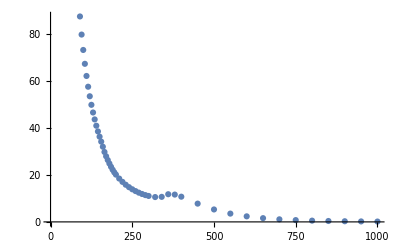

```mathematica
ListPlot[hxswg1]
```

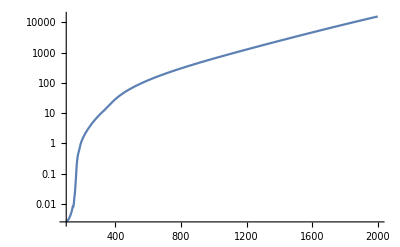

```mathematica
LogPlot[hwidth[x],{x,100,2000}]
```

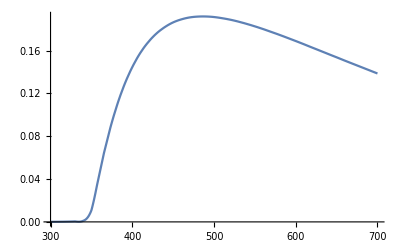

```mathematica
Plot[ttBRs[x],{x,300,700}]
```

```mathematica
wwBRs[wwbr[[5,1]]]
wwbr[[5,2]]
```

0.5022

0.5022

```mathematica
(*Defining a function that makes a series expansion and then takes the coefficients at a given order*)
GetCoef[exp_,exp2_,n_]:=Series[exp,{exp2,0,n+1}]//SeriesCoefficient[#,n]//.SeriesCoefficient[x_,y_]->0&
```

```mathematica
(*Higgs doublet and its conjugate*)
Phi={{phip},{(v+H+I*A0)/Sqrt[2]}}
Phic={phim,(v+H-I*A0)/Sqrt[2]}
```

{{phip},{(ⅈ A0+H+v)/(√2)}}

{phim,(-ⅈ A0+H+v)/(√2)}

```mathematica
Phic.Phi
```

{phim phip+1/2 (-ⅈ A0+H+v) (ⅈ A0+H+v)}

```mathematica
(*Defining the potential with two additional scalars*)
Pot=-μH^2*(Phic.Phi)[[1]]+λH*((Phic.Phi)[[1]])^2+λHS*((Phic.Phi)[[1]])*S^2-μS^2/2*S^2+λS*S^4-μs^2/2*s^2+λs*s^4+λsH*s^2/2*((Phic.Phi)[[1]])+λsS/4*s^2*S^2
```

(phim phip+1/2 (-ⅈ A0+H+v) (ⅈ A0+H+v))^2 λH+S^2 (phim phip+1/2 (-ⅈ A0+H+v) (ⅈ A0+H+v)) λHS+s^4 λs+S^4 λS+1/2 s^2 (phim phip+1/2 (-ⅈ A0+H+v) (ⅈ A0+H+v)) λsH+1/4 s^2 S^2 λsS-(phim phip+1/2 (-ⅈ A0+H+v) (ⅈ A0+H+v)) μH^2-(s^2 μs^2)/2-(S^2 μS^2)/2

```mathematica
(*Additional singlets acquiring a VEV*)
PotU=Pot//.{A0->0,phip->0,phim->0,S->vs+SS,s->vss+ss}//Expand;
```

```mathematica
(*Taking the first order terms in each field and solving for fluctuations around zero to minimise the potential*)
zerofluc={ss->0,H->0,SS->0,H1->0,H2->0,H3->0};
```

```mathematica
μHSol=Solve[(GetCoef[PotU,H,1]//.zerofluc)==0,μH][[2]]
```

{μH→(√(2 v^2 λH+2 vs^2 λHS+vss^2 λsH))/(√2)}

```mathematica
μSSol=Solve[(GetCoef[PotU,SS,1]//.zerofluc)==0,μS][[2]]
```

{μS→(√(2 v^2 λHS+8 vs^2 λS+vss^2 λsS))/(√2)}

```mathematica
μsSol=Solve[(GetCoef[PotU,ss,1]//.zerofluc)==0,μs][[2]]
```

{μs→(√(8 vss^2 λs+v^2 λsH+vs^2 λsS))/(√2)}

```mathematica
PotUmin=PotU//.μHSol//.μSSol//.μsSol//Expand;
```

```mathematica
(*Taking derivatives wrt fields of the potential*)
H11=D[D[PotU,H],H];
H12=D[D[PotU,H],SS];
H13=D[D[PotU,H],ss];
H21=D[D[PotU,SS],H];
H22=D[D[PotU,SS],SS];
H23=D[D[PotU,SS],ss];
H31=D[D[PotU,ss],H];
H32=D[D[PotU,ss],SS];
H33=D[D[PotU,ss],ss];
```

```mathematica
(*Getting a matrix of the masses*)
```

```mathematica
Hess={{H11,H12,H13},{H21,H22,H23},{H31,H32,H33}};
```

```mathematica
Hessmin=Hess//.μHSol//.μSSol//.μsSol//.zerofluc//Simplify
```

{{2 v^2 λH,2 v vs λHS,v vss λsH},{2 v vs λHS,8 vs^2 λS,vs vss λsS},{v vss λsH,vs vss λsS,8 vss^2 λs}}

```mathematica
Hessmin//.zerofluc
```

{{2 v^2 λH,2 v vs λHS,v vss λsH},{2 v vs λHS,8 vs^2 λS,vs vss λsS},{v vss λsH,vs vss λsS,8 vss^2 λs}}

```mathematica
m11=2*GetCoef[PotU,H,2]//.zerofluc//Simplify
m22=2*GetCoef[PotU,SS,2]//.zerofluc//Simplify
m33=2*GetCoef[PotU,ss,2]//.zerofluc//Simplify
m12=(GetCoef[PotU,H,1]//GetCoef[#,SS,1]&)//.zerofluc
m13=(GetCoef[PotU,H,1]//GetCoef[#,ss,1]&)//.zerofluc
m23=(GetCoef[PotU,SS,1]//GetCoef[#,ss,1]&)//.zerofluc
```

3 v^2 λH+vs^2 λHS+(vss^2 λsH)/2-μH^2

v^2 λHS+12 vs^2 λS+(vss^2 λsS)/2-μS^2

1/2 (24 vss^2 λs+v^2 λsH+vs^2 λsS-2 μs^2)

2 v vs λHS

v vss λsH

vs vss λsS

```mathematica
mass2matrixd2={{m11,m12,m13},{m12,m22,m23},{m13,m23,m33}}//.μHSol//.μSSol//.μsSol;
```

```mathematica
mass2matrixd2//TraditionalForm
```

(3 λH v^2+1/2 (-2 λH v^2-2 λHS vs^2-λsH vss^2)+λHS vs^2+(λsH vss^2)/2 | 2 λHS v vs | λsH v vss
2 λHS v vs | λHS v^2+1/2 (-2 λHS v^2-8 λS vs^2-λsS vss^2)+12 λS vs^2+(λsS vss^2)/2 | λsS vs vss
λsH v vss | λsS vs vss | 8 λs vss^2)

```mathematica
(*Function which calculates the cascade decay width*)
cascadeD[coup_,m1_,m2_,m3_]:=(coup^2*Sqrt[(m1^2-(m2-m3)^2)*(m1^2-(m2+m3)^2)])/(16*m1^3*Pi);
```

```mathematica
Hms={{H1},{H2},{H3}};
```

```mathematica
(*Transformation matrix from model basis to mass eigenbasis*)
Rmatrix={{ca1*ca2,sa1*ca2,sa2},{-(ca1*sa2*sa3+sa1*ca3),ca1*ca3-sa1*sa2*sa3,ca2*sa3},{-ca1*sa2*ca3+sa1*sa3,-(ca1*sa3+sa1*sa2*ca3),ca2*ca3}}//.{ca1->Cos[a1],ca2->Cos[a2],ca3->Cos[a3],sa1->Sin[a1],sa2->Sin[a2],sa3->Sin[a3]}
```

{{Cos[a1] Cos[a2],Cos[a2] Sin[a1],Sin[a2]},{-Cos[a3] Sin[a1]-Cos[a1] Sin[a2] Sin[a3],Cos[a1] Cos[a3]-Sin[a1] Sin[a2] Sin[a3],Cos[a2] Sin[a3]},{-Cos[a1] Cos[a3] Sin[a2]+Sin[a1] Sin[a3],-Cos[a3] Sin[a1] Sin[a2]-Cos[a1] Sin[a3],Cos[a2] Cos[a3]}}

```mathematica
Transpose[Rmatrix].Rmatrix//Simplify[#,{a1∈Reals,a2∈Reals,a3∈Reals}]&
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
diagmatrix={{M32,0,0},{0,M22,0},{0,0,M12}}
```

{{M32,0,0},{0,M22,0},{0,0,M12}}

```mathematica
Rmatrix[[1,3]]
```

Sin[a2]

```mathematica
paramm={{3*v^2*λH + vs^2*λHS + (vss^2*λsH)/2 + (-2*v^2*λH - 2*vs^2*λHS - vss^2*λsH)/2, 2*v*vs*λHS, v*vss*λsH}, 
 {2*v*vs*λHS, v^2*λHS + 12*vs^2*λS + (vss^2*λsS)/2 + (-2*v^2*λHS - 8*vs^2*λS - vss^2*λsS)/2, vs*vss*λsS}, 
 {v*vss*λsH, vs*vss*λsS, 8*vss^2*λs}};
```

```mathematica
set=Solve[Rmatrix.diagmatrix.Transpose[Rmatrix]==paramm,{λHS,λS,λsS,λHS,λsH,λH,λs}]
```

{{λHS→-1/(2 v vs)(-M22 Cos[a1] Cos[a2] Cos[a3] Sin[a1]+M32 Cos[a1] Cos[a2] Cos[a3] Sin[a1]-M12 Cos[a2] Sin[a2] Sin[a3]+M32 Cos[a1]^2 Cos[a2] Sin[a2] Sin[a3]+M22 Cos[a2] Sin[a1]^2 Sin[a2] Sin[a3]),λS→1/(8 vs^2)(M12 Cos[a2]^2 Sin[a3]^2+M32 (-Cos[a3] Sin[a1]-Cos[a1] Sin[a2] Sin[a3])^2+M22 (Cos[a1] Cos[a3]-Sin[a1] Sin[a2] Sin[a3])^2),λsS→1/(vs vss)(M12 Cos[a2]^2 Cos[a3] Sin[a3]+M32 (-Cos[a1] Cos[a3] Sin[a2]+Sin[a1] Sin[a3]) (-Cos[a3] Sin[a1]-Cos[a1] Sin[a2] Sin[a3])+M22 (-Cos[a3] Sin[a1] Sin[a2]-Cos[a1] Sin[a3]) (Cos[a1] Cos[a3]-Sin[a1] Sin[a2] Sin[a3])),λsH→-1/(v vss)(-M12 Cos[a2] Cos[a3] Sin[a2]+M32 Cos[a1]^2 Cos[a2] Cos[a3] Sin[a2]+M22 Cos[a2] Cos[a3] Sin[a1]^2 Sin[a2]+M22 Cos[a1] Cos[a2] Sin[a1] Sin[a3]-M32 Cos[a1] Cos[a2] Sin[a1] Sin[a3]),λH→-(-M32 Cos[a1]^2 Cos[a2]^2-M22 Cos[a2]^2 Sin[a1]^2-M12 Sin[a2]^2)/(2 v^2),λs→1/(8 vss^2)(M12 Cos[a2]^2 Cos[a3]^2+M22 (-Cos[a3] Sin[a1] Sin[a2]-Cos[a1] Sin[a3])^2+M32 (-Cos[a1] Cos[a3] Sin[a2]+Sin[a1] Sin[a3])^2)}}

```mathematica
scan={};
Do[
(*Ranges for the parameters - Maybe have a play with the mass ranges*)
param={M12->125^2,M22->(173*2+Random[]*200)^2,M32->(Sqrt[M12]+Sqrt[M22]+Random[]*500)^2,v->246,vs->3*Random[]*246,vss->3*Random[]*246,a1->-π/2+π*Random[],a2->π/2*(1-0.2*Random[]),a3->-π/2+π*Random[]};
setl=set[[1]]//.param;

mass2matrixd2l=(Rmatrix.diagmatrix.Transpose[Rmatrix])//.param//.setl;

rrr={{M32//.param,M22//.param,M12//.param},Transpose[Rmatrix]//.param};(*Eigensystem[mass2matrixd2l//.param];*)

(*find 125 GeV candidate*)
index=0;
Do[If[Abs[Sqrt[Abs[rrr[[1]][[i]]]]-125]<1,index=i],{i,1,3}];

(*check min of potential*)
Hessmatrixtest=(*PositiveDefiniteMatrixQ[Hessmin//.param//.setl];*)
(Eigenvalues[Hessmin//.param//.setl][[1]]>0&&Eigenvalues[Hessmin//.param//.setl][[2]]>0&&Eigenvalues[Hessmin//.param//.setl][[3]]>0);


(*scan criteria*)
If[Hessmatrixtest&&Sqrt[Abs[rrr[[1]][[1]]]]<1000,
If[Abs[rrr[[2]][[index,1]]]^2>0.90 (*SMlike Higgs which is lightest*)
(*&&Sqrt[Abs[rrr[[1]][[1]]]]>Sqrt[Abs[rrr[[1]][[2]]]]+Sqrt[Abs[rrr[[1]][[3]]]](*cascade is open - enforced by mass choices*)*),

(*Potential with the fields and eigenvectors*)
NPot=(PotUmin//.param//.setl//.{H:>Sum[rrr[[2]][[i,1]]*Hms[[i]],{i,1,3}],SS:>Sum[rrr[[2]][[i,2]]*Hms[[i]],{i,1,3}],ss:> Sum[rrr[[2]][[i,3]]*Hms[[i]],{i,1,3}]})[[1]]//Simplify;

(*Masses and couplings*)
m1=Sqrt[Abs[rrr[[1]][[1]]]];
m2=Sqrt[Abs[rrr[[1]][[2]]]];
m3=Sqrt[Abs[rrr[[1]][[3]]]];

(*Mass ratio as a measure of how open the cascade is for finding regions that give high BR*)
mrat = (m2 +m3) / m1;

trilinearH3H2H1=-((GetCoef[NPot,H1,1]//GetCoef[#,H2,1]&)//GetCoef[#,H3,1]&)//.zerofluc;
trilinearH3H1H1=-2*((GetCoef[NPot,H3,1]//GetCoef[#,H1,2]&))//.zerofluc;
trilinearH3H2H2=-2*((GetCoef[NPot,H3,1]//GetCoef[#,H2,2]&))//.zerofluc;
trilinearH3H3H2=-2*((GetCoef[NPot,H3,2]//GetCoef[#,H2,1]&))//.zerofluc;
trilinearH3H3H1=-2*((GetCoef[NPot,H3,2]//GetCoef[#,H1,1]&))//.zerofluc;
trilinearH2H1H1=-2*((GetCoef[NPot,H2,1]//GetCoef[#,H1,2]&))//.zerofluc;
trilinearH2H2H1=-2*((GetCoef[NPot,H2,2]//GetCoef[#,H1,1]&))//.zerofluc;
trilinearH3H3H3=-6*(GetCoef[NPot,H3,3])//.zerofluc;
trilinearH2H2H2=-6*(GetCoef[NPot,H2,3])//.zerofluc;
trilinearH1H1H1=-6*(GetCoef[NPot,H1,3])//.zerofluc;


(*Decay widths and branching fractions*)
SMlikedecay=hwidth[m1]*(Abs[rrr[[2]][[1,1]]])^2;
If[m1>2*m3,cascade33=cascadeD[trilinearH3H1H1,m1,m3,m3]/2,cascade33=0;];
If[m1>2*m2,cascade22=cascadeD[trilinearH3H2H2,m1,m2,m2]/2,cascade22=0;];
If[m1>m2+m3,cascade23=cascadeD[trilinearH3H2H1,m1,m2,m3],cascade23=0;];
Totaldec=SMlikedecay+cascade33+cascade22+cascade23;
BRcascade=cascade23/Totaldec;
crossm1=crosssec[m1]*(Abs[rrr[[2]][[1,1]]])^2;

SMlikedecay2=hwidth[m2]*(Abs[rrr[[2]][[2,1]]])^2;
If[m2>2*m1,cascade233=cascadeD[trilinearH2H1H1,m2,m3,m3]/2,cascade233=0;];
Totaldec2=SMlikedecay2+cascade233;
TopDec2=ttBRs[m2]*hwidth[m2]*(Abs[rrr[[2]][[2,1]]])^2;
       TopBR2=TopDec2/Totaldec2;
crossm2=crosssec[m2]*(Abs[rrr[[2]][[2,1]]])^2;

Totaldec3=hwidth[m3]*(Abs[rrr[[2]][[3,1]]])^2;

(*Checks and printing*)
If[crossm1*BRcascade*TopBR2 > 2,
Print[Sqrt[Abs[rrr[[1]][[1]]]],",  ",Sqrt[Abs[rrr[[1]][[2]]]],",  ",Sqrt[Abs[rrr[[1]][[3]]]],",  ", mrat, ",  ", trilinearH3H2H1,",  ",trilinearH3H3H3,",  ", trilinearH3H3H2,",  ", trilinearH3H3H1,",  ", trilinearH3H2H2,",  ", trilinearH3H1H1,",  ",trilinearH2H2H1,",  ",trilinearH2H1H1,",  ",trilinearH2H2H2, ",  ",trilinearH1H1H1, ",  ",BRcascade, ",  ", crossm1*BRcascade,",  ",crossm1*BRcascade*TopBR2,",  ",crossm1*BRcascade*TopBR2*2/9*2/9*0.6*1*1];

scan=Append[scan,{Sqrt[rrr[[1]][[1]]],Sqrt[rrr[[1]][[2]]],Sqrt[rrr[[1]][[3]]],mrat, trilinearH3H2H1,trilinearH3H3H3, trilinearH3H3H2, trilinearH3H3H1, trilinearH3H2H2, trilinearH3H1H1,trilinearH2H2H1,trilinearH2H1H1,trilinearH2H2H2, trilinearH1H1H1,rrr[[2]][[1,1]],rrr[[2]][[2,1]],rrr[[2]][[3,1]],Totaldec,Totaldec2,Totaldec3,λHS//.param//.setl,λsH//.param//.setl,λsS//.param//.setl,λH//.param//.setl,λS//.param//.setl,λs//.param//.setl,vs//.param//.setl,vss//.param//.setl,BRcascade,crossm2*TopBR2, crossm1*BRcascade*TopBR2*2/9*2/9*0.6*1*1}]];

]]


,{i,1,1000}]
```

526.684,  389.031,  125,  0.975975,  362.055,  -179.086,  56.2923,  -141.058,  -321.377,  -439.444,  1662.21,  -986.128,  -1133.22,  1905.62,  0.139114,  18.9601,  2.37965,  0.0705081

767.887,  434.929,  125,  0.729181,  4652.57,  -181.544,  -201.316,  -244.553,  -3507.58,  -3895.55,  70732.,  -64438.,  -67540.1,  47396.5,  0.642569,  15.4113,  2.76299,  0.0818663

647.41,  429.221,  125,  0.85606,  747.959,  -181.925,  25.0274,  -313.598,  440.323,  561.176,  -10352.3,  -12210.5,  -9112.08,  -11403.2,  0.47764,  20.6605,  3.6293,  0.107535

674.643,  462.614,  125,  0.871,  580.158,  -172.353,  -75.759,  -507.469,  260.668,  157.052,  -1790.92,  -3720.42,  -2500.58,  -1880.11,  0.283709,  21.9947,  4.17166,  0.123605

806.37,  448.065,  125,  0.710672,  -1354.28,  -179.575,  81.6408,  -339.299,  -1458.79,  -1726.87,  7965.97,  3954.93,  8847.67,  6041.74,  0.352798,  10.8757,  2.01836,  0.0598034

647.044,  496.804,  125,  0.960992,  776.187,  -174.065,  -284.802,  -381.604,  1530.01,  166.509,  -5641.52,  -3084.46,  -12496.4,  196.805,  0.470264,  21.5043,  4.11861,  0.122033

841.975,  476.696,  125,  0.714625,  1436.65,  -155.128,  -395.338,  -944.416,  1333.07,  257.337,  -5226.98,  -5965.04,  -7270.21,  1688.36,  0.594164,  13.8021,  2.64348,  0.0783254

658.807,  505.045,  125,  0.956342,  -1506.06,  -157.348,  -585.763,  -10.157,  2702.44,  54.6299,  8444.5,  -2662.3,  -19682.1,  4205.96,  0.833131,  24.566,  4.68722,  0.138881

```mathematica
(*Cutting out points with |λ| > π*) 
scanpicut = Cases[scan, {_,_,_,_,_,_,_,_,_,_,_,_,_,_,_?(Abs[#] < Pi &),_?(Abs[#] < Pi &),_?(Abs[#] < Pi &),_?(Abs[#] < Pi &),_?(Abs[#] < Pi &),_?(Abs[#] < Pi &),_,_,_,_,_}];
Print["Points satisfying σ×BRs criteria: ", Length[scan]]
Print["Points remaining after π cut: ",Length[scanpicut]]
```

Points satisfying σ×BRs criteria: 568

Points remaining after π cut: 110

```mathematica
Export["/Users/oliveratkinson/Documents/PhD/Research/ssinglet.dat", scan]
```

/Users/oliveratkinson/Documents/PhD/Research/ssinglet.dat

```mathematica
SelectData[x_,k_,m_]:=(Drop[x,None,{m+1,25}]//Drop[#,None,{1,k-1}]&)//Drop[#,None,{2,m-k}]&
```

```mathematica
SelectData[scanpicut,5,25];
```

```mathematica
scan[[All,{25}]];
```

```mathematica
(*Picking out the points with the highest cross section after all BR factors*)
highpos = Ordering[scanpicut[[All,{25}]],-20 ];
highscan = scanpicut[[highpos]];
highscan[[All, 25]]
Median[highscan[[All, 25]]]
```

{0.101448,0.103898,0.106372,0.108703,0.110523,0.112252,0.113254,0.114411,0.117804,0.118612,0.121772,0.122931,0.125537,0.130009,0.131766,0.133031,0.137254,0.138236,0.145918,0.185074}

0.120192

```mathematica
(*Checking the λs just to be sure*)
If[Max[highscan[[All, {15, 16, 17, 18, 19, 20}]]]> Pi, Print["At least one λ is too large"], Print["All λ are fine"]]
```

All λ are fine

```mathematica
Export["/Users/oliveratkinson/Documents/PhD/Research/ssinglet_high.dat",highscan]
```

```mathematica
"/Users/oliveratkinson/Documents/PhD/Research/ssinglet_high.dat"
```

/Users/oliveratkinson/Documents/PhD/Research/ssinglet_high.dat

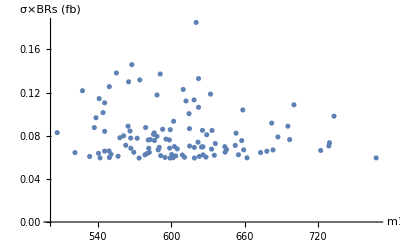

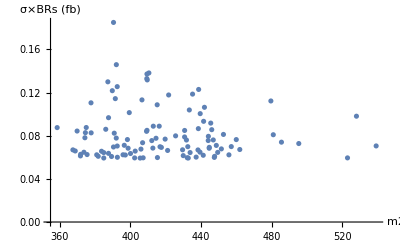

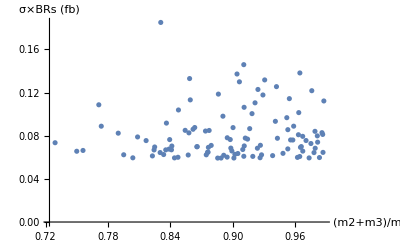

```mathematica
(*Plotting to check where maximal cross sections can be found and find any relations*)
ListPlot[SelectData[scanpicut,1,25], AxesLabel->{"m1","σ×BRs (fb)"}]
ListPlot[SelectData[scanpicut,2,25], AxesLabel->{"m2","σ×BRs (fb)"}] 
ListPlot[SelectData[scanpicut,4,25], AxesLabel->{"(m2+m3)/m1","σ×BRs (fb)"}]
```

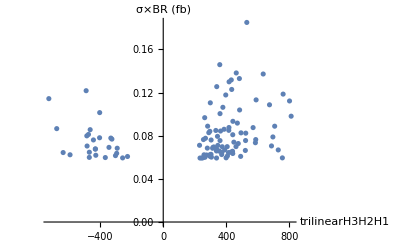

```mathematica
ListPlot[SelectData[scanpicut,5,25], AxesLabel->{"trilinearH3H2H1","σ×BR (fb)"}]
```

```mathematica
ListPointPlot3D[scanpicut[[All,{1, 2, 25}]], AxesLabel->{"m1","m2","σ×BRs (fb)" }]
```

-Graphics3D-